```mathematica
var1= 1+121/304 e^2 ;
p = p0(e/e0)^(12/19) (var1/(var1/.e->e0))^(870/2299)  ;
dedt = e/p 1/p^3(1-e^2)^(3/2)var1    //PowerExpand //Simplify
```

((1-e^2)^(3/2) e0^(48/19) (1+(121 e0^2)/304)^(3480/2299))/(e^(29/19) (1+(121 e^2)/304)^(1181/2299) p0^4)

General::munfl: 0.0000204286^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^68 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204286^70 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

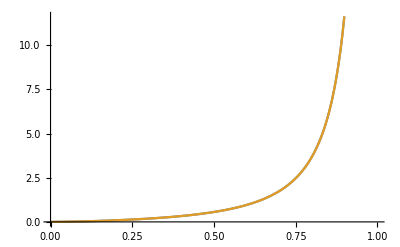

```mathematica
var2 =( ((1-e^2)^(3/2))/(e^(29/19) (1+(121 e^2)/304)^(1181/2299)))^-1 ;
var2Exp = Series[var2,{e,0,200}] //Normal //N //Simplify   ;
Plot[{var2,var2Exp},{e,0,1}]
```